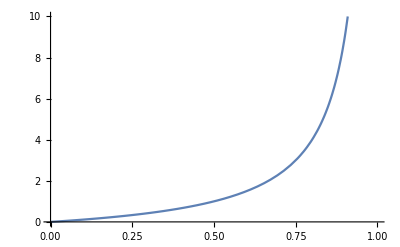

```mathematica
Plot[x/(1-x),{x,0,1},PlotRange->{0,10}]
```

```mathematica
x=1/2
N[x/(1-x)]
```

1/2

1.

```mathematica
Sum[x^i,{i,1,∞}]
```

-x/(-1+x)

```mathematica
∝
```

```mathematica
f[θ_,ρ_]:= ρ/(1-ρ)*Cos[θ]
g[θ_,ρ_]:= ρ*Cos[θ]
albedo=0.5*{0.9,0.8,0.2};
test=Table[Table[10*f[(x*π/2)/512,albedo],{x,0,512}],{y,0,32}];
Image[test]
```

-Graphics-

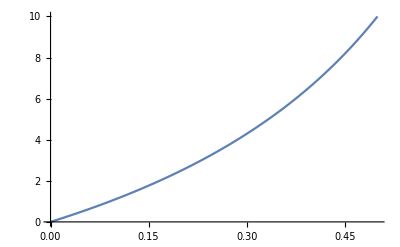

```mathematica
Plot[f[10,x],{x,0,0.5}]
```

```mathematica
Manipulate[
albedo=r*0.5*{0.9,0.7,0.2};
test=Table[Table[10*f[(x*π/2)/512,albedo],{x,0,512}],{y,0,32}];
Image[test]
,{{r,1.0},0,1}]
```

```mathematica
Manipulate[
albedo=r*0.5*{0.9,0.7,0.2};
test=Table[Table[10*g[(x*π/2)/512,albedo],{x,0,512}],{y,0,32}];
Image[test]
,{{r,1.0},0,1}]
```

### Go!

```mathematica
albedo=r*0.5*{0.9,0.7,0.2};
test=Table[Table[10*f[(x*π/2)/512,albedo],{x,0,512}],{y,0,32}];
Image[test]
```